# Fit Data in Time-Growth and Time-Kill

### Time Kill

```mathematica
logN={8.23, 4.96,4.48, 3.64}
time={0,1,2,3}
```

{8.23,4.96,4.48,3.64}

{0,1,2,3}

```mathematica
data=Table[{time[[i]],logN[[i]]},{i,1,4}]
```

{{0,8.23},{1,4.96},{2,4.48},{3,3.64}}

```mathematica
timeKill=LinearModelFit[data,x/Log[10],x]
```

FittedModel[7.465-1.425 x]

```mathematica
bandTimeKill[t_]:=timeKill["MeanPredictionBands"]
```

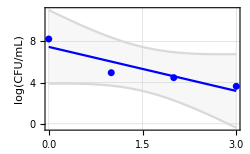

```mathematica
temp1=Plot[timeKill[x],{x,0,time[[-1]]},GridLines->Automatic,
PlotStyle->Blue];
temp2=ListPlot[data,
PlotStyle->{Blue,PointSize[0.02]},
GridLines->Automatic];
temp3=Plot[Evaluate[bandTimeKill[t]],{x,0,time[[-1]]},
ImageSize->250,
PlotRange->All,
BaseStyle->"Medium",
GridLines->Automatic,
PlotStyle->LightGray,
Frame->True,
FrameLabel->{"Time, h","log(CFU/mL)"},
Filling->{1->{2}}
];
(*Show[temp1,temp2]*)
Show[temp3,temp2,temp1]
```

```mathematica
timeKill["BestFitParameters"]
Knon=timeKill["BestFitParameters"][[2]]
```

{7.465,-3.28118}

-3.28118

```mathematica
timeKill["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 7.465 | 0.830856 | 8.9847 | 0.0121622
x/Log[10] | -3.28118 | 1.0226 | -3.20865 | 0.0849381

### Time Growth

```mathematica
timeTimeGrowth={0,2,4,6}
logNTimeGrowth={7.39,8.45,9.09,9.12}
```

{0,2,4,6}

{7.39,8.45,9.09,9.12}

```mathematica
dataTimeGrowth=Table[{timeTimeGrowth[[i]],logNTimeGrowth[[i]]},{i,1,4}]
```

{{0,7.39},{2,8.45},{4,9.09},{6,9.12}}

```mathematica
(*sol=DSolve[{c'[t]==Kg*c[t](1-c[t]/10^logNmax),c[0]==10^logN0},c[t],t]*)
sol=DSolve[{c'[t]==Kg*c[t](1-c[t]/cmax),c[0]==c0},c[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c[t]→(c0 cmax ⅇ^(Kg t))/(-c0+cmax+c0 ⅇ^(Kg t))}}

```mathematica
fit[t_]:=(Log10[c[t]])/.sol[[1]]
```

```mathematica
(*timeGrowth=NonlinearModelFit[dataTimeGrowth,fit[t],{{Kg,0.5},{logN0,7},{logNmax,9}},t]*)
timeGrowth=NonlinearModelFit[dataTimeGrowth,
(*{fit[t],2>Kg>0.5,10^8>c0>10^7,10^10>cmax>10^9},*)
fit[t],
{{Kg,1.35},{c0,2*10^7},{cmax,1.4*10^9}},
t(*,
Method->"ConjugateGradient"*)
(*AccuracyGoal->20,
PrecisionGoal->20,*)
(*MaxIterations->1000*)]
```

FittedModel[Log[(3.43986×10^16 ⅇ^(«19» t))/(1.39871×10^9+«22» ⅇ^(«1»))]/Log[10]]

```mathematica
timeGrowth
```

FittedModel[Log[(3.43986×10^16 ⅇ^(«19» t))/(1.39871×10^9+«22» ⅇ^(«1»))]/Log[10]]

```mathematica
bandTimeGrowth[t_]:=timeGrowth["MeanPredictionBands"]
```

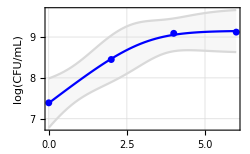

```mathematica
temp1=Plot[timeGrowth[t],{t,0,timeTimeGrowth[[-1]]},GridLines->Automatic,
PlotStyle->Blue];
temp2=ListPlot[dataTimeGrowth,
PlotStyle->{Blue,PointSize[0.02]},
GridLines->Automatic];
temp3=Plot[Evaluate[bandTimeGrowth[t]],{t,0,timeTimeGrowth[[-1]]},
ImageSize->250,
PlotRange->All,
BaseStyle->"Medium",
GridLines->Automatic,
PlotStyle->LightGray,
Frame->True,
FrameLabel->{"Time, h","log(CFU/mL)"},
Filling->{1->{2}}
];
(*Show[temp1,temp2]*)
Show[temp3,temp2,temp1]
```

```mathematica
timeGrowth
```

FittedModel[Log[(3.43986×10^16 ⅇ^(«19» t))/(1.39871×10^9+«22» ⅇ^(«1»))]/Log[10]]

1.35427

7.38337

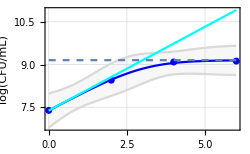

```mathematica
Knoff=Kg/.timeGrowth["BestFitParameters"]
log10N0=Log10[c0]/.timeGrowth["BestFitParameters"]
temp4=Plot[log10N0+Knoff/Log[10]*t,
{t,0,timeTimeGrowth[[-1]]},
PlotStyle->{Cyan}];
temp5=Plot[Log10[cmax]/.timeGrowth["BestFitParameters"],
{t,0,timeTimeGrowth[[-1]]},
PlotStyle->{Dashed}];
Show[temp3,temp2,temp1,temp4,temp5]
```

```mathematica
timeGrowth["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
Kg | 1.35427 | 0.0878799 | 15.4105 | 0.0412531
c0 | 2.41753×10^7 | 2.64536×10^6 | 9.13875 | 0.0693855
cmax | 1.42288×10^9 | 1.39758×10^8 | 10.181 | 0.0623301

```mathematica
timeGrowth["BestFitParameters"]
Knoff=Kg/.%[[1]]
```

{Kg→1.35427,c0→2.41753×10^7,cmax→1.42288×10^9}

1.35427

```mathematica
Rn=Knon/Knoff
toffton=Rn/(Rn-2)
```

-2.42284

0.547802

```mathematica
timeGrowth["CorrelationMatrix"];
MatrixForm[%]
```

(1. | -0.610896 | -0.436767
-0.610896 | 1. | 0.12257
-0.436767 | 0.12257 | 1.)

### General

```mathematica
DSolve[{c'[t]==Kn*c[t]*(1-c[t]/cmax),c[0]==c0},c[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c[t]→(c0 cmax ⅇ^(Kn t))/(-c0+cmax+c0 ⅇ^(Kn t))}}

```mathematica
-3.8/1.34
```

-2.83582